```mathematica
data1992={0,34,67,101,135,202,259,336,404,471,15.18,21.36,25.72,32.29,34.03,39.45,43.15,43.46,40.83,30.75,0,24,49,73,98,147,196,245,294,342,33.46,32.47,36.06,37.96,41.04,40.09,41.26,42.17,40.36,42.73,0,47,93,140,186,279,372,465,558,651,18.98,27.35,34.86,38.52,38.44,37.73,38.43,43.87,42.77,46.22};
len=Length[data1992]/6;
```

```mathematica
data1992N=Table[data1992[[{i,i+len}]],{i,1,10}]
data1992P=Table[data1992[[{i+2len,i+3len}]],{i,1,10}]
data1992K=Table[data1992[[{i+4len,i+5len}]],{i,1,10}]
```

{{0,15.18},{34,21.36},{67,25.72},{101,32.29},{135,34.03},{202,39.45},{259,43.15},{336,43.46},{404,40.83},{471,30.75}}

{{0,33.46},{24,32.47},{49,36.06},{73,37.96},{98,41.04},{147,40.09},{196,41.26},{245,42.17},{294,40.36},{342,42.73}}

{{0,18.98},{47,27.35},{93,34.86},{140,38.52},{186,38.44},{279,37.73},{372,38.43},{465,43.87},{558,42.77},{651,46.22}}

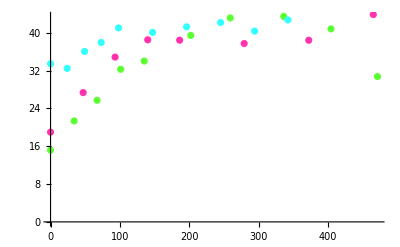

```mathematica
pointN=ListPlot[data1992N,PlotStyle->Hue[0.3,0.8,1]];
pointP=ListPlot[data1992P,PlotStyle->Hue[0.5,0.8,1]];
pointK=ListPlot[data1992K,PlotStyle->Hue[0.9,0.8,1]];
Show[pointN,pointK,pointP]
```

```mathematica
(*选择合适的函数方程进行拟合N元素*)
modelForN=b*x+a*x*x+c;
approxN=FindFit[data1992N,{modelForN},{a,b,c},x];
paramsN=modelForN/.approxN
approxNfunc=Plot[paramsN,{x,0,500},PlotStyle->Red];
```

14.7416+0.19715 x-0.000339532 x^2

```mathematica
(*选择合适的函数方程进行拟合P元素*)
approxP=Fit[data1992P,{1,Sin[0.048x],x,x^2,x^3},x]
approxPfunc=Plot[approxP,{x,0,350},PlotStyle->Blue];
```

32.8132+0.0938964 x-0.000336117 x^2+4.03747×10^-7 x^3-1.46516 Sin[0.048 x]

```mathematica
(*选择合适的函数方程进行拟合K元素*)
modelForK=0.1*(h*Log[a,f*x+g])+c+d*Sin[e*x+b];
control={a>150,f>0.2,f<0.4,g>2,g<4,Abs[e]<0.06};
approxK=FindFit[data1992K,{modelForK,control},{a,b,c,d,e,f,g,h},x];
paramsK=modelForK/.approxK
approxKfunc=Plot[paramsK,{x,0,700},PlotStyle->Green];
```

13.2296+6.2206 Log[3.40072+0.235672 x]+2.07181 Sin[5.14214-0.0224003 x]

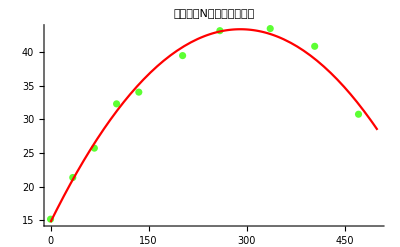

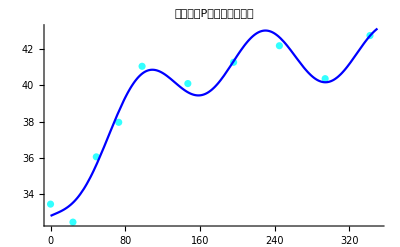

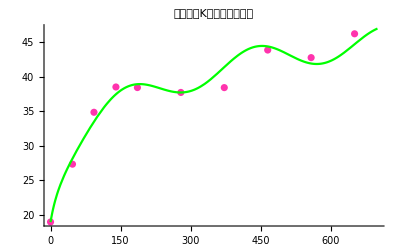

```mathematica
(*绘图*)
Show[{pointN,approxNfunc},PlotRange->All,PlotLabel->"生菜的施N量与产量的拟合"]
Show[{pointP,approxPfunc},PlotRange->All,PlotLabel->"生菜的施P量与产量的拟合"]
Show[{pointK,approxKfunc},PlotRange->All,PlotLabel->"生菜的施K量与产量的拟合"]
```

```mathematica
(*计算N的相关系数*)
factN=Transpose[data1992N][[2]];
predictionN=Table[paramsN/.{x->data1992N[[i,1]]},{i,1,len}];
Correlation[factN,predictionN]
```

0.993122

```mathematica
(*计算P的相关系数*)
factP=Transpose[data1992P][[2]];
predictionP=Table[approxP/.{x->data1992P[[i,1]]},{i,1,len}];
Correlation[factP,predictionP]
```

0.988268

```mathematica
(*计算K的相关系数*)
factP=Transpose[data1992K][[2]];
predictionP=Table[paramsK/.{x->data1992K[[i,1]]},{i,1,len}];
Correlation[factP,predictionP]
```

0.986489